We first define constants based on exponential regression fits to fidelity from the Sycamore data (Fig. 1) and extrapolated error rates (Fig. S1). Constants from the Summit supercomputer are used to characterize classical simulation performance times.

```mathematica
(* noise constants *)
Clear[l,g]
errorProgress=0.774;
l[yearsFromNow_]:=0.0043*errorProgress^yearsFromNow
g[yearsFromNow_]:=0.042*errorProgress^yearsFromNow

(* SFA constants *)
Clear[k]
k[p_]:=1/2+1/p
b=0.24;

(* runtime constants, in units of 10^15 Hz *)
Clear[csa,cq,csfa]
(*csa[yearsFromNow_]:=0.015*1.74^yearsFromNow*)
csa[yearsFromNow_]:=0.015
cq[yearsFromNow_]:=N[10^6*20/200/10^15]
(*csfa[yearsFromNow_]:=3.3*1.74^yearsFromNow*)
csfa[yearsFromNow_]:=3.3
```

We find the boundary of TN performance for n=53 qubits using exponential regression fits to NVIDIA Quadro P2000 simulations of circuits from m=12 to m=20.

```mathematica
(* determine TN advantage data point *)
fidelity[n_,m_,t_]:=2^(-(l[t] m(3n/2-Sqrt[n]/2)+g[t] n))
tnRuntimeF53Seconds[m_,t_]:=(8.17*10^-11)Exp[2.38m] fidelity[53,m,t]
(* quantum runtime, in years *)
quantumRuntime[n_,m_,t_]:=QuantityMagnitude[UnitConvert[Quantity[1/(10^15*cq[t])*2^(2l[t](3n/2-Sqrt[n]/2)m+2g[t] n)*m,"Seconds"],"Years"]]
(* quantum runtime, in seconds *)
quantumRuntimeSeconds[n_,m_,t_]:=quantumRuntime[n,m,t]*Quantity[1,"Years"]/Quantity[1,"Seconds"]
(* solve at what circuit size TN gains an advantage *)
NSolve[tnRuntimeF53Seconds[m,0]==quantumRuntimeSeconds[53,m,0]&&5<m<20,m]
```

{{m→11.0144}}

SA and SFA classical algorithm runtimes and scalings are defined. For SFA, we also define a function that optimizes the number of patches, requiring at least p=2 patches.

```mathematica
(* runtimes *)
sfaFraction[n_,m_,p_,t_]:=(1/(Round[p] 2^(n/Round[p])))^(1/2)
(*sfaFraction[n_,m_,p_,t_]:=2^(-(l[t] m(3n/2-Sqrt[n]/2)+g[t] n))*)
SFAc[n_,m_,p_,t_]:=Log2[(sfaFraction[n,m,p,t] 2^(k[p] Round[p] b n^0.5 m+n/Round[p]+Log2[Round[p]])+Min[1/sfaFraction[n,m,p,t]^2,2^n] 2^(k[p] Round[p] b n^0.5 m)sfaFraction[n,m,p,t])/csfa[t]/(2^(2(l[t] m(3n/2-Sqrt[n]/2)+g[t] n)+Log2[m])/cq[t])]
SAc[n_,m_,t_]:=Log2[2^(n+Log2[n m]-Log2[csa[t]])/2^(2(l[t] m(3n/2-Sqrt[n]/2)+g[t] n)+Log2[m]-Log2[cq[t]])]
SFAoptc[n_,m_,t_]:=NMinimize[{Log2[(sfaFraction[n,m,p,t] 2^(k[p] Round[p] b n^0.5 m+n/Round[p]+Log2[Round[p]])+Min[1/sfaFraction[n,m,p,t]^2,2^n] 2^(k[p] Round[p] b n^0.5 m)sfaFraction[n,m,p,t])/csfa[t]/(2^(2(l[t] m(3n/2-Sqrt[n]/2)+g[t] n)+Log2[m])/cq[t])],2≤p≤10&&p∈Integers},p,AccuracyGoal->2,MaxIterations->50][[1]]
```

```mathematica
(* scalings *)
SFA[n_,m_,p_,t_]:=Log2[sfaFraction[n,m,p,t]2^(k[p] Round[p] b n^0.5 m+n/Round[p]+Log2[Round[p]])+Min[1/sfaFraction[n,m,p,t]^2,2^n] 2^(k[p] Round[p] b n^0.5 m)sfaFraction[n,m,p,t]]/(2(l[t] m(3n/2-Sqrt[n]/2)+g[t] n)+Log2[m])-1
SA[n_,m_,t_]:=(n+Log2[n m])/(2(l[t] m(3n/2-Sqrt[n]/2)+g[t] n)+Log2[m])-1
SFAopt[n_,m_,t_]:=NMinimize[{Log2[sfaFraction[n,m,p,t]2^(k[p] Round[p] b n^0.5 m+n/Round[p]+Log2[Round[p]])+Min[1/sfaFraction[n,m,p,t]^2,2^n] 2^(k[p] Round[p] b n^0.5 m)sfaFraction[n,m,p,t]]/(2(l[t] m(3n/2-Sqrt[n]/2)+g[t] n)+Log2[m])-1,2≤p≤10&&p∈Integers},p,AccuracyGoal->2,MaxIterations->50][[1]]
```

Limitations of classical hardware in memory and number of cores are calculated, as well as the resulting limitations on circuit sizes tolerated by SA and SFA. Not used in the paper, we also have commented extrapolations of supercomputer parameters. Since increasing circuit size increases memory requirements far faster than supercomputer memory increases over time, accounting for such extrapolations leaves the results largely unchanged.

```mathematica
(* qubit sizes *)
Clear[memory,SAqubits,SFAqubits]
(*memory[yearsFromNow_]:=3*2^50*1.44^yearsFromNow*)
memory[yearsFromNow_]:=3*2^50
(*cores[yearsFromNow_]:=10^6*1.43^yearsFromNow*)
cores[yearsFromNow_]:=10^6
SAqubits[t_]:=Floor[NSolve[2^(n+1)==memory[t]&&n>0,n][[1,1,2]]]
(*SFAqubits[p_,t_]:=Floor[NSolve[10^6 2^(n/p+1)==memory[t]&&n>0,n][[1,1,2]]]*)
SFAqubits[p_,t_]:=Floor[Round[p](-1+Log[memory[t]/cores[t]]/Log[2])]
```

We now set up helper labels for the plotting functions.

```mathematica
(* plotting ranges *)
minm=5;
maxm=500;
minn=10;
maxn=1000;

(* hacky way to generate nice y axis labels *)
y1=Table[{Log[10^i],10^i},{i,Floor[Log10[minn]],Floor[Log10[maxn]]}];
y2=Table[{Log[5*10^i],5*10^i},{i,Floor[Log10[minn]],Floor[Log10[maxn]]}];
yticks=Join[y1,y2];
x1=Table[{Log[10^i],Rotate[ToString[10^i],45Degree]},{i,Floor[Log10[minm]],Floor[Log10[maxm]]}];
x2=Table[{Log[5*10^i],Rotate[ToString[5*10^i],45Degree]},{i,Floor[Log10[minm]],Floor[Log10[maxm]]}];
xticks=Join[x1,x2];
```

Starting with memory-limited analysis of the main text, we create contours for the quantum, SA, and SFA runtimes with memory limitations.

```mathematica
(* quantum runtime contours *)
quantumContours[t_]:=ContourPlot[quantumRuntime[n,m,t],{m,minm,maxm},{n,minn,maxn},PlotRange->{{minm,maxm},{minn,maxn}},ScalingFunctions->{"Log","Log"},Contours->{Quantity[1,"Seconds"]/Quantity[1,"Year"],1/365,100},ContourStyle->{{Thickness[0.005],RGBColor[0.0,0.0,0.0],Opacity[1.0]},{Thickness[0.005],RGBColor[0.0,0.0,0.0],Opacity[1.0]}},ContourShading->False,FrameLabel->{"# of cycles (m)","# of qubits (n)"},LabelStyle->{FontSize->16,FontFamily->"CMU Serif"},PlotPoints->50]
```

```mathematica
(* SA runtime contours *)
saContours[t_]:=RegionPlot[SAc[Exp[n],Exp[m],t]<0,{m,Log[minm],Log[maxm]},{n,Log[minn],Log[SAqubits[t]]},PlotRange->{{Log[minm],Log[maxm]},{Log[minn],Log[maxn]}},FrameTicks->{{yticks,None},{xticks,None}},PlotStyle->Opacity[0.6,RGBColor[0.43,0.64,0.35]],BoundaryStyle->None,FrameLabel->{"# of cycles (m)","# of qubits (n)"},LabelStyle->{FontSize->16,FontFamily->"CMU Serif",FontColor->Black}]
```

```mathematica
(* SFA runtime contours *)
sfaContours[t_]:=RegionPlot[(SFAc[Exp[n],Exp[m],2,t]<0&&n<Log[SFAqubits[2,t]])||(SFAc[Exp[n],Exp[m],3,t]<0&&n<Log[SFAqubits[3,t]])||(SFAc[Exp[n],Exp[m],4,t]<0&&n<Log[SFAqubits[4,t]])||(SFAc[Exp[n],Exp[m],5,t]<0&&n<Log[SFAqubits[5,t]])||(SFAc[Exp[n],Exp[m],6,t]<0&&n<Log[SFAqubits[6,t]])||(SFAc[Exp[n],Exp[m],7,t]<0&&n<Log[SFAqubits[7,t]])||(SFAc[Exp[n],Exp[m],8,t]<0&&n<Log[SFAqubits[8,t]])||(SFAc[Exp[n],Exp[m],9,t]<0&&n<Log[SFAqubits[9,t]])||(SFAc[Exp[n],Exp[m],10,t]<0&&n<Log[SFAqubits[10,t]])||(SFAc[Exp[n],Exp[m],11,t]<0&&n<Log[SFAqubits[11,t]])||(SFAc[Exp[n],Exp[m],12,t]<0&&n<Log[SFAqubits[12,t]])||(SFAc[Exp[n],Exp[m],13,t]<0&&n<Log[SFAqubits[13,t]])||(SFAc[Exp[n],Exp[m],14,t]<0&&n<Log[SFAqubits[14,t]])||(SFAc[Exp[n],Exp[m],15,t]<0&&n<Log[SFAqubits[15,t]]),{m,Log[minm],Log[maxm]},{n,Log[minn],Log[maxn]},PlotRange->{{Log[minm],Log[maxm]},{Log[minn],Log[maxn]}},FrameTicks->{{yticks,None},{xticks,None}},PlotStyle->Opacity[0.6,RGBColor[0.93,0.60,0.33]],BoundaryStyle->None]
```

```mathematica
plotContours[t_]:=Show[saContours[t],sfaContours[t],quantumContours[t],Epilog->{RGBColor[0.77,0.31,0.28],PointSize@Medium,Join[{Point[{Log[12],Log[53]}],Point[{Log[14],Log[53]}],Point[{Log[16],Log[53]}],Point[{Log[18],Log[53]}],Point[{Log[20],Log[53]}]},Table[Point[{Log[14],Log[2i]}],{i,6,19}],Table[Point[{Log[14],Log[i]}],{i,39,53}]]}]
```

We include the TN boundary from above at n=53 qubits.

```mathematica
cross=Graphics[{Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}];
tnAdvantage[t_]:=ListPlot[{{Log[NSolve[tnRuntimeF53Seconds[m,t]==quantumRuntimeSeconds[53,m,t]&&5<m<20,m][[1,1,2]]],Log[53]}},PlotMarkers->{cross,0.05}]
```

We plot Fig. 4.

```mathematica
nFunc[t_,c_]:=NSolve[quantumRuntime[n,√n,t]==c&&n>0,n][[1,1,2]]
nPlots=Table[ListLogLinearPlot[Table[{errorProgress^t,nFunc[t,c]},{t,0,10,0.1}],PlotRange->{Automatic,{0,1000}},Joined->True,Frame->{True,True,False,False},FrameLabel->{"ϵ × Sycamore error","n = m^2"},LabelStyle->{FontSize->16,FontFamily->"CMU Serif",FontColor->Black},AspectRatio->1],{c,{Quantity[1,"Seconds"]/Quantity[1,"Year"],1/365,100}}];
```

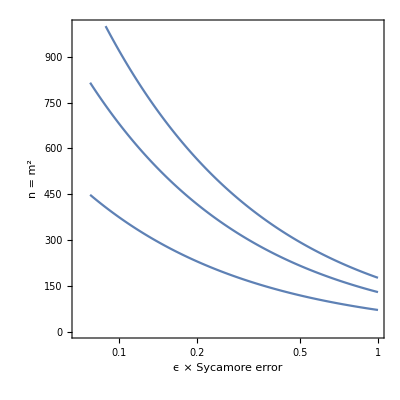

```mathematica
Show[nPlots[[1]],nPlots[[2]],nPlots[[3]]]
```

And now we can plot the figures 3(b), 3(c), and 3(a).

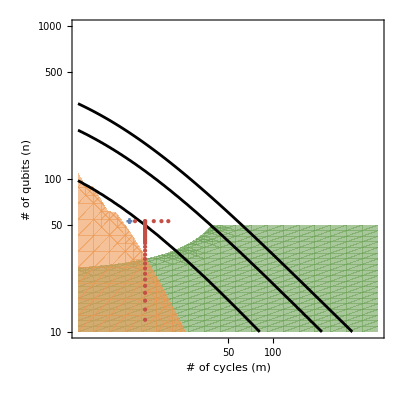

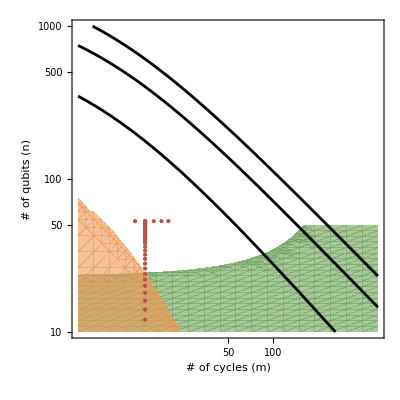

```mathematica
l[yearsFromNow_]:=0.0043*errorProgress^yearsFromNow
g[yearsFromNow_]:=0.042*errorProgress^yearsFromNow
f3b=Show[plotContours[0],tnAdvantage[0]]
f3c=plotContours[5]
```

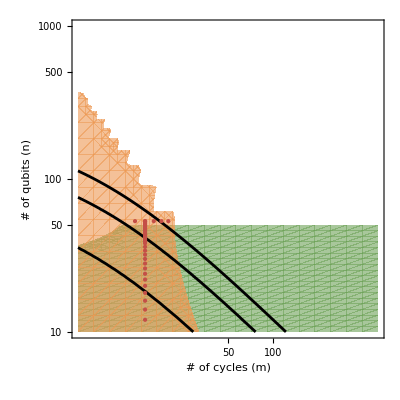

```mathematica
l[yearsFromNow_]:=2.77*0.0043*errorProgress^yearsFromNow
g[yearsFromNow_]:=2.77*0.042*errorProgress^yearsFromNow
f3a=plotContours[0]
l[yearsFromNow_]:=0.0043*errorProgress^yearsFromNow
g[yearsFromNow_]:=0.042*errorProgress^yearsFromNow
```

```mathematica
(* PDF export to avoid rasterization in Mathematica 12: Export["fig.pdf",Graphics[Inset[f3c,Automatic,Automatic,Scaled[1]]]] *)
```

Define the plotting ranges for Fig. 2.

```mathematica
(* plotting ranges *)
minm=5;
maxm=10000;
minn=10;
maxn=10000;

(* hacky way to generate nice y axis labels *)
y1=Table[{Log[10^i],10^i},{i,Floor[Log10[minn]],Floor[Log10[maxn]]}];
y2=Table[{Log[5*10^i],5*10^i},{i,Floor[Log10[minn]],Floor[Log10[maxn]]}];
yticks=Join[y1,y2];
x1=Table[{Log[10^i],Rotate[ToString[10^i],45Degree]},{i,Floor[Log10[minm]],Floor[Log10[maxm]]}];
x2=Table[{Log[5*10^i],Rotate[ToString[5*10^i],45Degree]},{i,Floor[Log10[minm]],Floor[Log10[maxm]]}];
xticks=Join[x1,x2];
```

First we plot SA, including both the time scaling (SA[]) and the runtime (SAc[]).

```mathematica
sa1=ContourPlot[SA[n,m,0],{m,minm,maxm},{n,minn,maxn},PlotLegends->BarLegend[Automatic,LegendLabel->"α_SA",LabelStyle->{FontSize->16,FontFamily->"CMU Serif"}],ScalingFunctions->{"Log","Log"},Contours->Table[-2+i,{i,0,14}],FrameLabel->{"m","n"},LabelStyle->{FontSize->16,FontFamily->"CMU Serif"}];
sa2=ContourPlot[SA[n,m,0],{m,minm,maxm},{n,minn,maxn},ScalingFunctions->{"Log","Log"},Contours->{0},ContourStyle->{Thickness[0.02],RGBColor[1,0.2,0.2]},ContourShading->False];
sa3=ContourPlot[SAc[n,m,0],{m,minm,maxm},{n,minn,maxn},ScalingFunctions->{"Log","Log"},Contours->{0},ContourStyle->{Dashed,Thickness[0.01],RGBColor[0.0,0.9,0.0],Opacity[1.0]},ContourShading->False];
```

Now we plot SFA, optimizing the number of patches (requiring at least two patches).

```mathematica
sfa1=ContourPlot[SFAopt[n,m,0],{m,minm,maxm},{n,minn,maxn},PlotLegends->BarLegend[Automatic,LegendLabel->"α_SFA",LabelStyle->{FontSize->16,FontFamily->"CMU Serif"}],ScalingFunctions->{"Log","Log"},Contours->Table[-2+i,{i,0,10}],FrameLabel->{"m","n"},LabelStyle->{FontSize->16,FontFamily->"CMU Serif"}];
```

```mathematica
sfa2=ContourPlot[SFAopt[n,m,0],{m,minm,maxm},{n,minn,maxn},ScalingFunctions->{"Log","Log"},Contours->{0},ContourStyle->{Thickness[0.02],RGBColor[1,0.2,0.2]},ContourShading->False];
```

```mathematica
sfa3=ContourPlot[SFAoptc[n,m,0],{m,minm,maxm},{n,minn,maxn},ScalingFunctions->{"Log","Log"},Contours->{0},ContourStyle->{Dashed,Thickness[0.01],RGBColor[0.0,0.9,0.0],Opacity[1.0]},ContourShading->False];
```

```mathematica
Show[sfa1,sfa2,sfa3,sa3,Epilog->{Green,PointSize@Medium,Join[{Point[{Log[12],Log[53]}],Point[{Log[14],Log[53]}],Point[{Log[16],Log[53]}],Point[{Log[18],Log[53]}],Point[{Log[20],Log[53]}]},Table[Point[{Log[14],Log[2i]}],{i,6,19}],Table[Point[{Log[14],Log[i]}],{i,39,53}]]}]
```

```mathematica
Show[sa1,sa2,sa3,sfa3,Epilog->{Green,PointSize@Medium,Join[{Point[{Log[12],Log[53]}],Point[{Log[14],Log[53]}],Point[{Log[16],Log[53]}],Point[{Log[18],Log[53]}],Point[{Log[20],Log[53]}]},Table[Point[{Log[14],Log[2i]}],{i,6,19}],Table[Point[{Log[14],Log[i]}],{i,39,53}]]}]
```